## Graphene Band structure along the high symmetry points

### First we start with δ-vectors of Graphene which connect the atoms to their nearest neighbours(a = 1)

```mathematica
Subscript[δ, 1]={1/2,(√3)/2};
Subscript[δ, 2]={1/2,-(√3)/2};
Subscript[δ, 3]={-1,0};
a= 1;
t = 1;
```

The tight-binding Hamiltonian for graphene can be written as: ℋ̂=∑_(k⃗) ψ†(k⃗)𝒽̂(k⃗)ψ(k⃗), for 𝒽̂(k⃗)=(0 | f(k⃗)
f*(k⃗) | 0), Where, f(k⃗)=-t∑_δ exp(i k⃗,δ⃗)
Now, we  can  write f(k⃗)= -t(e^(ik⃗.δ⃗)) = -t(e^-ik_xa+2 e^(ik_x a/2)Cos(k_y a√3/2))

```mathematica
f = -t(Exp[-I kx a]+2Exp[I kx a /2]Cos[ky a √3/2]);
```

```mathematica
fc = -t(Exp[I kx a]+2Exp[-I  kx a /2]Cos[ky a √3/2]); (*conjugate of f*)
```

```mathematica
h = {{0,f},{fc,0}}
```

{{0,-ⅇ^(-ⅈ kx)-2 ⅇ^((ⅈ kx)/2) Cos[(√3 ky)/2]},{-ⅇ^(ⅈ kx)-2 ⅇ^(-(ⅈ kx)/2) Cos[(√3 ky)/2],0}}

```mathematica
h // MatrixForm
```

(0 | -ⅇ^(-ⅈ kx)-2 ⅇ^((ⅈ kx)/2) Cos[(√3 ky)/2]
-ⅇ^(ⅈ kx)-2 ⅇ^(-(ⅈ kx)/2) Cos[(√3 ky)/2] | 0)

```mathematica
evals = Eigenvalues[h]
```

{-ⅇ^(-ⅈ kx) √(3 ⅇ^(2 ⅈ kx)+2 ⅇ^((ⅈ kx)/2) Cos[(√3 ky)/2]+2 ⅇ^((7 ⅈ kx)/2) Cos[(√3 ky)/2]+2 ⅇ^(2 ⅈ kx) Cos[√3 ky]),ⅇ^(-ⅈ kx) √(3 ⅇ^(2 ⅈ kx)+2 ⅇ^((ⅈ kx)/2) Cos[(√3 ky)/2]+2 ⅇ^((7 ⅈ kx)/2) Cos[(√3 ky)/2]+2 ⅇ^(2 ⅈ kx) Cos[√3 ky])}

```mathematica
e1 = evals[[1]]
```

-ⅇ^(-ⅈ kx) √(3 ⅇ^(2 ⅈ kx)+2 ⅇ^((ⅈ kx)/2) Cos[(√3 ky)/2]+2 ⅇ^((7 ⅈ kx)/2) Cos[(√3 ky)/2]+2 ⅇ^(2 ⅈ kx) Cos[√3 ky])

```mathematica
e2 = evals[[2]]
```

ⅇ^(-ⅈ kx) √(3 ⅇ^(2 ⅈ kx)+2 ⅇ^((ⅈ kx)/2) Cos[(√3 ky)/2]+2 ⅇ^((7 ⅈ kx)/2) Cos[(√3 ky)/2]+2 ⅇ^(2 ⅈ kx) Cos[√3 ky])

```mathematica
Plot3D[{e1,e2},{kx,-3,3},{ky,-3,3},BoxRatios->{1, 1, 1},AxesLabel->Automatic]
```

-Graphics3D-

### We can use the above obtained eigenvalues to get the plot along the desired path as well. Here we will use the exact expression which we know from literature to plot that.

```mathematica
a = 1;
E1 = Sqrt[1 + 4*Cos[3*kx*a/2]*Cos[Sqrt[3] ky*a/2] + 4*Cos[Sqrt[3]*ky*a/2]^2]
```

√(1+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+4 Cos[(√3 ky)/2]^2)

### Now we generate the path along which we want to calculate the band structure. The following function generates a klist along which we have to calculate the energy eigenvalues of the Hamiltonian.

GenerateKpath:
 INPUT:
	Parameter 	| 	Description
	nk			|	Number of points between high symmetry points (default = 50)
	{x1,y1,z1}		| 	List containing the coordinates of first point
	{x2,y2,z2}		|	List containing the coordinates of second point
	
OUTPUT:
	Returns a list containing nk number of points inside a list

```mathematica
(*Generate k-path list*)
GenerateKpath[nk_:50,{x1_,y1_,z1_},{x2_,y2_,z2_}]:=
Module[{numK=nk,initialx=x1,initialy=y1,initialz=y1,finalx=x2,finaly=y2,finalz=z2},
Clear[i];
klist={};
For[i=0,i≤nk-1,i++,
klist=Append[klist,{initialx,initialy,initialz}+i/numK*({finalx,finaly,finalz}-{initialx,initialy,initialz})]
];
Return[klist]
]
```

### Here we are taking the path Γ -> M -> K -> Γ

```mathematica
kPathFull={};
nPoints= 50;
klist1=GenerateKpath[nPoints,{0,0,0},{2*(Pi/3),0,0}]; (* Γ->M *)
klist2=GenerateKpath[nPoints,{2*(Pi/3),0,0},{2*Pi/3,2*Pi/(3√3),0}]; (* M->K *)
klist3=GenerateKpath[nPoints,{2*Pi/3,2*Pi/(3√3),0},{0,0,0}]; (* K->Γ *)
kPathFull=Join[klist1,klist2,klist3]; (* Γ->M->K->Γ *)
```

PlotEnergies:
	INPUT:
		parameter	|	Description
		enList		| 	List containing the expression of energies to be plotted
	Remark : This works for two expressions of energies but it is very straight-forward to generalise it for any number of energies.
	
	OUTPUT:
		It returns the plot of energy spectrum along the given path.

```mathematica
PlotEnergies[enList_]:=({
For[i=1,i≤Length[kPathFull],i++,
	res1 = ReplaceAll[enList[[1]],  {kx-> kPathFull[[i,1]],ky-> kPathFull[[i,2]]}];
	res2 = ReplaceAll[enList[[2]],  {kx-> kPathFull[[i,1]],ky-> kPathFull[[i,2]]}];
AppendTo[ev1,res1];
AppendTo[ev2,res2];
];
ListLinePlot[{ev1,ev2},Ticks->{{{0,"Γ"},{50,"M"},{100,"K"},{150,"Γ"}},{Max[ev1],Min[ev2]}},AxesLabel->{None,HoldForm[Energy]},PlotLabel->HoldForm[Graphene Tight Binding],LabelStyle->{FontFamily->"Iosevka",GrayLevel[0]},TicksStyle->Directive[Red, Bold]]
})
```

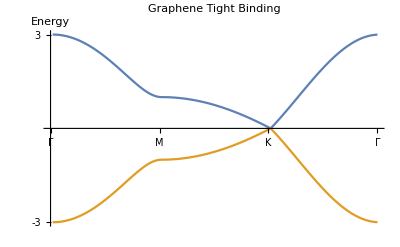

```mathematica
ev1={};
ev2={};
enList={E1,-E1};
PlotEnergies[enList][[1]]
```